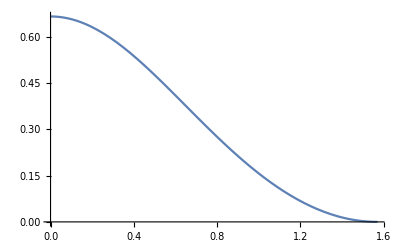

```mathematica
Plot[4/3 Pi / (2Pi/3*(Tan[(Pi/2-θ)/2]^2 + Cot[(Pi/2-θ)/2]^2+1)),{θ,0,Pi/2}]
```

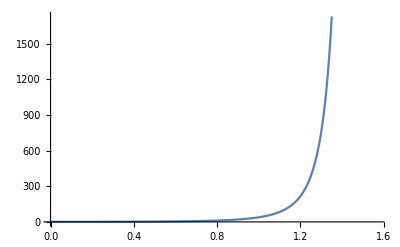

```mathematica
Plot[(Pi/3 *(2+Cos[Pi/2-θ])(1-Cos[Pi/2-θ])^2+Pi/3 *(Sec[θ]+Tan[θ])^6 *(2+Cos[Pi/2+θ])(1-Cos[Pi/2+θ])^2)/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),{θ,0,Pi/2}]
```

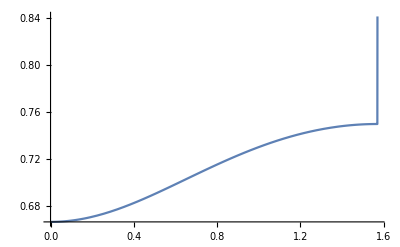

```mathematica
Plot[((Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ])))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),{θ,0,Pi/2}]
```

```mathematica
(Sec[30 Degree]+Tan[30 Degree])^2
```

3

```mathematica
(2+Cos[2Pi/3])(1-Cos[2Pi/3])^2
```

27/8

```mathematica
h1=1-Cos[Pi/3]
```

1/2

```mathematica
h2=2-h1
```

3/2

```mathematica
Pi*h1^2/3 * (3-h1)+Pi*h2^2/3 * (3-h2)
```

(4 π)/3

```mathematica
4/3 Pi / (2Pi/3*(Tan[(Pi/2-θ)/2]^2 + Cot[(Pi/2-θ)/2]^2+1))/.θ->Pi/3 // N
```

0.133333

```mathematica
(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))) /.θ->Pi/3// N
```

0.733333

```mathematica
FullSimplify[4/3 Pi / (2Pi/3*(Tan[(Pi/2-θ)/2]^2 + Cot[(Pi/2-θ)/2]^2+1)),0<=θ<=Pi/2]
```

-(4 Cos[θ]^2)/(-7+Cos[2 θ])

```mathematica
FullSimplify[(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))) ,0<=θ<=Pi/2]
```

1+2/(-7+Cos[2 θ])

```mathematica
(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))) /. θ->Pi/4 // N
```

3.9456

```mathematica
(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])) /. θ->Pi/4 // N
```

48.1512

```mathematica
(Sec[θ]+Tan[θ])^2 /. θ->Pi/4
```

(1+√2)^2

```mathematica
Pi*(1/Sqrt[2]+1)^2/3*(3*(1+√2)^2-(1/Sqrt[2]+1)) // N
```

48.1512

```mathematica
1/3*Pi*(1/Sqrt[2]+1+1+1/Sqrt[2])*((Sqrt[2]/2)^2+(Sqrt[2]/2)(1+√2)^2/Sqrt[2]+((1+√2)^2/Sqrt[2])^2)//N
```

72.9355

```mathematica
Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))/.θ->Pi/4 // N
```

72.9355

```mathematica
CP[a_,A_,x0_,B_,y0_,C_,z0_]:=Module[{D,z,aa,bb,cc},D=-A x0-B y0-C z0;aa=(A^2+B^2+C^2) Sin[a °]^2-C^2;bb=-2 C D;cc=-D^2;z=(-bb+√(bb^2-4 aa cc))/(2 aa);Return[{z,z Sin[a °]}]]
CS[a_,x1_,y1_,z1_,r1_]:=Module[{aa,bb,cc,z,s1},s1=1;aa=1-Sin[a °]^2;bb=-2 z1-2 s1 r1 Sin[a °];cc=x1^2+y1^2+z1^2-r1^2;z=Min[(-bb+√(bb^2-4 aa cc))/(2 aa),(-bb-√(bb^2-4 aa cc))/(2 aa)];Return[{0,0,z,z Sin[a °]}]]
csss[x1_,y1_,z1_,r1_,x2_,y2_,z2_,r2_,x3_,y3_,z3_,r3_,an_]:=Module[{m,n,A,B,C,D,E,F,a,x,y,z,r,xyzs,zs},
m={{-2 x1+2 x2,-2 y1+2 y2,-2 z1+2 z2,-2 r1+2 r2,-x1^2+x2^2-y1^2+y2^2-z1^2+z2^2+r1^2-r2^2},{-2 x2+2 x3,-2 y2+2 y3,-2 z2+2 z3,-2 r2+2 r3,-x2^2+x3^2-y2^2+y3^2-z2^2+z3^2+r2^2-r3^2}};n=RowReduce[m];A=n⟦1,5⟧;B=n⟦1,4⟧;C=n⟦1,3⟧;D=n⟦2,5⟧;E=n⟦2,4⟧;F=n⟦2,3⟧;
a=an ;
r=Min[r/.{ToRules[Reduce[((1/(2 (C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2))(2 A C Cos[a]^2+2 D F Cos[a]^2-2 B C r Cos[a]^2-2 ⅇ F r Cos[a]^2-2 r Sin[a])-1/(2 (1+C^2+F^2))(2 A C+2 D F-2 B C r-2 ⅇ F r-2 C x1-2 F y1+2 z1))^2-1/(4(1+C^2+F^2)^2)((-2 A C-2 D F+2 B C r+2 ⅇ F r+2 C x1+2 F y1-2 z1)^2-4 (1+C^2+F^2) (A^2+D^2-2 A B r-2 D ⅇ r-r^2+B^2 r^2+ⅇ^2 r^2-2 r r1-r1^2-2 A x1+2 B r x1+x1^2-2 D y1+2 ⅇ r y1+y1^2+z1^2))-1/(4(C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2)^2)((-2 A C Cos[a]^2-2 D F Cos[a]^2+2 B C r Cos[a]^2+2 ⅇ F r Cos[a]^2+2 r Sin[a])^2-4 (-r^2+A^2 Cos[a]^2+D^2 Cos[a]^2-2 A B r Cos[a]^2-2 D ⅇ r Cos[a]^2+B^2 r^2 Cos[a]^2+ⅇ^2 r^2 Cos[a]^2) (C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2)))^2-4*1/(4(1+C^2+F^2)^2)((-2 A C-2 D F+2 B C r+2 ⅇ F r+2 C x1+2 F y1-2 z1)^2-4 (1+C^2+F^2) (A^2+D^2-2 A B r-2 D ⅇ r-r^2+B^2 r^2+ⅇ^2 r^2-2 r r1-r1^2-2 A x1+2 B r x1+x1^2-2 D y1+2 ⅇ r y1+y1^2+z1^2))*1/(4(C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2)^2)((-2 A C Cos[a]^2-2 D F Cos[a]^2+2 B C r Cos[a]^2+2 ⅇ F r Cos[a]^2+2 r Sin[a])^2-4 (-r^2+A^2 Cos[a]^2+D^2 Cos[a]^2-2 A B r Cos[a]^2-2 D ⅇ r Cos[a]^2+B^2 r^2 Cos[a]^2+ⅇ^2 r^2 Cos[a]^2) (C^2 Cos[a]^2+F^2 Cos[a]^2-Sin[a]^2))==0,r,Reals, Quartics->True]]}];
Return[r]
]
```

```mathematica
csss[0,0,Csc[θ]-1-(Sec[θ]+Tan[θ])^2,1,((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Sin[0],((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Cos[0],Csc[θ]-1-(Sec[θ]+Tan[θ])^2+1/2 √((1+Cos[a]-Tan[a/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Sin[2*ArcSin[1/(2+Cos[a])]],((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Cos[2*ArcSin[1/(2+Cos[a])]],Csc[θ]-1-(Sec[θ]+Tan[θ])^2+1/2 √((1+Cos[a]-Tan[a/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]+csss[0,0,Csc[θ],(Sec[θ]+Tan[θ])^2,1,((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Sin[0],((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Cos[0],Csc[θ]-1-(Sec[θ]+Tan[θ])^2+1/2 √((1+Cos[a]-Tan[a/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Sin[2*ArcSin[1/(2+Cos[a])]],((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]))*Cos[2*ArcSin[1/(2+Cos[a])]],Csc[θ]-1-(Sec[θ]+Tan[θ])^2+1/2 √((1+Cos[a]-Tan[a/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]
```

$Aborted

```mathematica
0,0,Csc[θ],(Sec[θ]+Tan[θ])^2,0,((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a])),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2
```

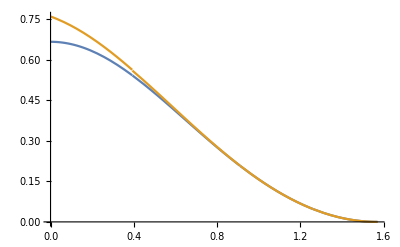

```mathematica
Plot[{((Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4)))*Pi*(Sin[Pi/2-θ])^3/(3Tan[θ])+Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ])))/(Pi*Cot[(Pi/2-θ)/2]^3/(3*Tan[θ])),
((Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ]))+4/3*Pi*((Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2)^3*Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])])/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4)))*Pi*(Sin[Pi/2-θ])^3/(3Tan[θ])+Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ])))/(Pi*Cot[(Pi/2-θ)/2]^3/(3*Tan[θ]))},{θ,0,Pi/2}]
```

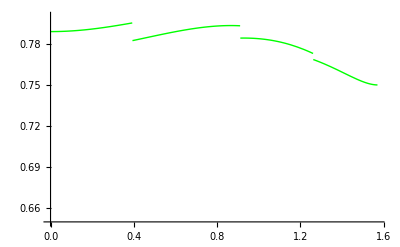

efficency.svg

```mathematica
Plot[{((Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ])))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ])))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),
(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ]))+4/3*Pi*((Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2)^3*Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])])/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),
(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ]))+4/3*Pi*((Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2)^3*Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])]+(4/3*Pi*csss[0,0,Csc[θ],1,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[0],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[0],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[2*ArcSin[1/(2+Cos[θ])]],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[2*ArcSin[1/(2+Cos[θ])]],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]^3+4/3*Pi*csss[0,0,Csc[θ]+1+(Sec[θ]+Tan[θ])^2,(Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[0],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[0],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[2*ArcSin[1/(2+Cos[θ])]],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[2*ArcSin[1/(2+Cos[θ])]],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]^3)*(Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])]-1))/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4)))},{θ,0.001,Pi/2-0.001},PlotRange->{0.65,0.8},PlotStyle->{Transparent,Transparent,Directive[Thick,Green]}]
Export["efficency.svg",%]
```

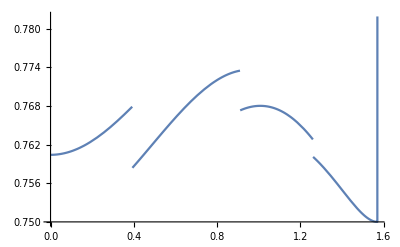

```mathematica
Plot[(Pi/3*(1+Cos[Pi/2-θ])^2*(3-(1+Cos[Pi/2-θ]))+(Sec[θ]+Tan[θ])^6*Pi/3*(1-Cos[Pi/2-θ])^2*(3-(1-Cos[Pi/2-θ]))+4/3*Pi*((Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2)^3*Floor[2 Pi/(2*ArcSin[1/(2+Cos[θ])])])/(Pi/3*(1+Cos[Pi/2-θ]+(Sec[θ]+Tan[θ])^2*(1-Cos[Pi/2-θ]))*((Sin[Pi/2-θ])^2*(1+(Sec[θ]+Tan[θ])^2+(Sec[θ]+Tan[θ])^4))),{θ,0,Pi/2}]
```

```mathematica
Plot[(csss[0,0,Csc[θ]+1+(Sec[θ]+Tan[θ])^2,(Sec[θ]+Tan[θ])^2,1,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[0],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[0],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[2*ArcSin[1/(2+Cos[θ])]],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[2*ArcSin[1/(2+Cos[θ])]],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2),(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2,θ]^3),{θ,0,Pi/2}]
```

-Graphics-

```mathematica
openCone[{{x1_,y1_,z1_},{x2_,y2_,z2_}},r_]:={CapForm[None],Tube[{{x1,y1,z1},{x2,y2,z2}},{r,0}]}
Manipulate[Show[
Graphics3D[{
Sphere[{0,0,Csc[θ]+1+(Sec[θ]+Tan[θ])^2},(Sec[θ]+Tan[θ])^2],
Sphere[{((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[0],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[0],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2)},(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2],
Sphere[{((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Sin[2*ArcSin[1/(2+Cos[θ])]],((2+Cos[θ]) (1+Sin[θ]))/(2 (1+Cos[θ]))*Cos[2*ArcSin[1/(2+Cos[θ])]],Csc[θ]+1/2 √((1+Cos[θ]-Tan[θ/2])^2)},(Sec[θ]+Tan[θ])^2/(1+Sec[θ]+Tan[θ])^2],
{Opacity[0.5],openCone[{{0,0,10},{0,0,0}},10*Tan[θ]]}
}
]],{{θ,Pi/8},0,Pi/4}]
```